## Diffusion

```mathematica
n=32;
maxIterations = 10;
relaxationIterations = 10;
vcycleDepth = 3;
a = 0.0;
b = 1.0;
diffusivity = 1.0;
deltaT = 1.0;
deltaX[n_]:= (b - a)/n;
M[n_]:= diffusivity*deltaT/deltaX[n]^2;
f[x_]:=Sin[2 π x];
x = Table[deltaX[n]*(i - 0.5),{i,1,n}];
fx = f[x];
A[n_]:=Module[{a},a=SparseArray[{Band[{1,1}]->2*M[n] + 1,Band[{2,1}]->-M[n],Band[{1,2}]->-M[n]},{n,n}];
a[[1,1]]=M[n]+1;
a[[n,n]]=M[n]+1;
a];
exactSolution = LinearSolve[A[n],fx];
LPlusU[n_]:=SparseArray[{Band[{2,1}]->-M[n],Band[{1,2}]->-M[n]},{n,n}];
Diag[n_]:=Module[{d},d=SparseArray[{Band[{1,1}]->2*M[n]+1},{n,n}];
d[[1,1]]=M[n]+1;
d[[n,n]]=M[n]+1;
d];
DInverse[n_]:=Module[{d},d=SparseArray[{Band[{1,1}]->1/(2*M[n]+1)},{n,n}];
d[[1,1]]=1/(M[n]+1);
d[[n,n]]=1/(M[n]+1);
d];
exactSolution = LinearSolve[A[n],fx];
Interpolate[q_]:=Flatten[Table[{q[[i]],q[[i]]},{i,1,Length[q]}]]
Restrict[q_]:=Table[(q[[2*i-1]] + q[[2*i ]])/2,{i,1,Length[q]/2}]

jacobiRelax[q_,rhs_]:=Module[{result = q,i},
For[i=0,i<relaxationIterations,i++,result = DInverse[Length[q]].(rhs - LPlusU[Length[q]].result );];
result
]
jacobiWeight = N[2/3];
weightedJacobiRelax[q_,rhs_]:=Module[{result=q,i,res},
For[i=0,i<maxIterations,i++,
res = rhs - A[Length[q]].result;
result= result +jacobiWeight*(DInverse[Length[result]].res);
];
Return[result];
]
Relax[q_,rhs_]:=weightedJacobiRelax[q,rhs];
```

```mathematica
testJacobi = jacobiRelax[fx, fx];
testWeightedJacobi = weightedJacobiRelax[fx, fx];
```

```mathematica
vcycle[q_,rhs_]:= Module[{q1,q2,q3,q4,rhs1,rhs2,rhs3,rhs4,residual,error},
q1 = q;
rhs1 = rhs;
q1 =Relax[q1, rhs1];
residual = rhs1 - A[Length[q1]].q1;
rhs2 =Restrict[residual];
q2 = ConstantArray[0.0,Length[rhs2]];
q2 = Relax[q2,rhs2];
residual =  rhs2 - A[Length[q2]].q2;
rhs3 = Restrict[residual];
q3=ConstantArray[0.0,Length[rhs3]];
q3 = Relax[q3,rhs3];
residual = rhs3 - A[Length[q3]].q3;
rhs4 = Restrict[residual];
q4 = LinearSolve[A[Length[rhs4]],rhs4];
error = Interpolate[q4];
q3 = q3 + error;
q3 = Relax[q3, rhs3];
error = Interpolate[q3];
q2 = q2 + error;
q2 = Relax[q2, rhs2];
error = Interpolate[q2];
q1 = q1 + error;
q1 = Relax[q1,rhs1];
q1
]
```

```mathematica
repeatedVcycles[q_,rhs_,m_]:=Module[{sol=q,i},
For[i=0,i<m,i++,
sol = vcycle[sol,rhs];];
sol
];
```

```mathematica
Norm[A[n].repeatedVcycles[fx,fx,1] - fx]
```

17.732

```mathematica
rr[m_]:=Norm[(A[n].sol[m] - fx)]
```

```mathematica
sol[m_]:=repeatedVcycles[fx,fx,m];
```

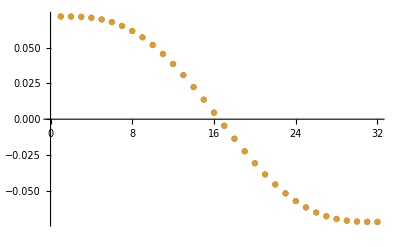

```mathematica
ListPlot[{exactSolution,sol[2]}]
```

```mathematica
rr[1]
```

0.451076

```mathematica
rr[2]
```

0.000902682

```mathematica
rr[3]
```

2.24798×10^-6

```mathematica
rr[4]
```

6.33552×10^-9

```mathematica
rr[5]
```

1.88188×10^-11

## V cycle

```mathematica
q1 = fx;
rhs1 = fx;
q1 =Relax[q1, rhs1];
```

```mathematica
fx
```

{0.0980171,0.290285,0.471397,0.634393,0.77301,0.881921,0.95694,0.995185,0.995185,0.95694,0.881921,0.77301,0.634393,0.471397,0.290285,0.0980171,-0.0980171,-0.290285,-0.471397,-0.634393,-0.77301,-0.881921,-0.95694,-0.995185,-0.995185,-0.95694,-0.881921,-0.77301,-0.634393,-0.471397,-0.290285,-0.0980171}

```mathematica
q1
```

{0.453275,0.474241,0.531879,0.613497,0.702638,0.783465,0.843701,0.875543,0.875114,0.841415,0.775447,0.679685,0.557803,0.414485,0.255239,0.0861835,-0.0861835,-0.255239,-0.414485,-0.557803,-0.679685,-0.775447,-0.841415,-0.875114,-0.875543,-0.843701,-0.783465,-0.702638,-0.613497,-0.531879,-0.474241,-0.453275}

```mathematica
residual = rhs1 - A[Length[q1]].q1
```

{21.1144,37.3675,24.4955,7.72393,-8.44295,-20.9868,-28.9617,-32.9261,-33.9485,-32.9286,-30.402,-26.6535,-21.8739,-16.2538,-10.009,-3.37964,3.37964,10.009,16.2538,21.8739,26.6535,30.402,32.9286,33.9485,32.9261,28.9617,20.9868,8.44295,-7.72393,-24.4955,-37.3675,-21.1144}

```mathematica
rhs2 =Restrict[residual]
```

{29.241,16.1097,-14.7149,-30.9439,-33.4385,-28.5277,-19.0639,-6.69434,6.69434,19.0639,28.5277,33.4385,30.9439,14.7149,-16.1097,-29.241}

Old

```mathematica
rhsList = {{0.00009571986360308653,0.00028348113013131087,0.0004603483758066383,0.00061952469156606,0.0007548930208620478,0.0008612512347151904,0.0009345120466134853,0.0009718600846408172,0.0009718600846408173,0.0009345120466134853,0.0008612512347151905,0.000754893020862048,0.00061952469156606,0.00046034837580663854,0.0002834811301313109,0.00009571986360308674,-0.00009571986360308651,-0.00028348113013131065,-0.0004603483758066383,-0.0006195246915660598,-0.0007548930208620475,-0.0008612512347151904,-0.0009345120466134852,-0.0009718600846408173,-0.0009718600846408173,-0.0009345120466134853,-0.0008612512347151905,-0.0007548930208620477,-0.0006195246915660605,-0.0004603483758066386,-0.00028348113013131103,-0.00009571986360308643},{0.0001896004968671987,0.0005399365336863492,0.000808072127788619,0.0009531860656271512,0.0009531860656271512,0.0008080721277886193,0.0005399365336863493,0.00018960049686719883,-0.0001896004968671986,-0.0005399365336863491,-0.0008080721277886189,-0.0009531860656271512,-0.0009531860656271512,-0.000808072127788619,-0.0005399365336863495,-0.00018960049686719873},{0.00036476851527677396,0.0008806290967078851,0.0008806290967078853,0.00036476851527677406,-0.00036476851527677385,-0.0008806290967078851,-0.0008806290967078851,-0.0003647685152767741},{0.0006226988059923296,0.0006226988059923296,-0.0006226988059923295,-0.0006226988059923296},{0.0006226988059923296,-0.0006226988059923296},{0.}};
```

### first v-cycle

```mathematica
sol = weightedJacobiRelax[{0},rhsList[[6]]]
```

{0.}

```mathematica
sol = Interpolate[sol]
```

### second v-cycle

```mathematica
sol = {0.,0.};
sol = weightedJacobiRelax[sol,rhsList[[5]]]
```

{0.00019159,-0.00019159}

#### relaxation

```mathematica
DInverseRes = DInverse[2].rhsList[[5]]
```

{0.000276755,-0.000276755}

```mathematica
result = sol + jacobiWeight*DInverseRes
```

{0.000184503,-0.000184503}

```mathematica
Asol = A[2].result
```

{0.000599636,-0.000599636}

```mathematica
res = rhsList[[5]] - Asol
```

{0.0000230629,-0.0000230629}

```mathematica
DInverseRes = DInverse[2].res
```

{0.0000102502,-0.0000102502}

```mathematica
result = result + jacobiWeight*DInverseRes
```

{0.000191337,-0.000191337}

```mathematica
Asol = A[2].result
```

{0.000621845,-0.000621845}

```mathematica
res = rhsList[[5]] - Asol
```

{8.54182×10^-7,-8.54182×10^-7}

```mathematica
DInverseRes = DInverse[2].res
```

{3.79637×10^-7,-3.79637×10^-7}

```mathematica
result = result + jacobiWeight*DInverseRes
```

{0.00019159,-0.00019159}

```mathematica
Asol = A[2].sol
```

{0.000622667,-0.000622667}

```mathematica
res = rhsList[[5]] - Asol
```

{3.16364×10^-8,-3.16364×10^-8}

```mathematica
rhs = Restrict[res]
```

{0.}

```mathematica
sol =weightedJacobiRelax[{0.},rhs]
```

{0.}

```mathematica
err = Interpolate[sol]
```

{0.,0.}

```mathematica
sol = {0.00019158989834321737,-0.00019158989834321737} + err
```

{0.00019159,-0.00019159}

```mathematica
sol = weightedJacobiRelax[sol,rhsList[[5]]]
```

{0.0001916,-0.0001916}

```mathematica
sol = Interpolate[sol]
```

{0.0001916,0.0001916,-0.0001916,-0.0001916}

### Third v-cycle

```mathematica
sol ={0.00019159963211847235,0.00019159963211847235,-0.00019159963211847235,-0.00019159963211847235};
sol = N[weightedJacobiRelax[sol,rhsList[[4]]],18]
```

{0.000433375,0.000332406,-0.000332406,-0.000433375}

```mathematica
Asol = A[4].sol
```

{0.00056143,0.000584618,-0.000584618,-0.00056143}

```mathematica
res = rhsList[[4]] - Asol
```

{0.0000612689,0.0000380813,-0.0000380813,-0.0000612689}

```mathematica
rhs = Restrict[res]
```

{0.0000496751,-0.0000496751}

```mathematica
sol = weightedJacobiRelax[{0.,0.},rhs]
```

{0.0000152839,-0.0000152839}

```mathematica
Asol = A[2].sol
```

{0.0000496726,-0.0000496726}

```mathematica
res = rhs - Asol
```

{2.52376×10^-9,-2.52376×10^-9}

```mathematica
rhs = Restrict[res]
```

{-6.77626×10^-21}

```mathematica
sol = weightedJacobiRelax[{0.},rhs]
```

{-2.1751×10^-21}

```mathematica
err = Interpolate[sol]
```

{-2.1751×10^-21,-2.1751×10^-21}

```mathematica
sol = {0.000015283870230865304,-0.000015283870230865334} + err
```

{0.0000152839,-0.0000152839}

```mathematica
sol = weightedJacobiRelax[sol,{0.0000496751020069554,-0.000049675102006955455}]
```

{0.0000152846,-0.0000152846}

```mathematica
err = Interpolate[sol]
```

{0.0000152846,0.0000152846,-0.0000152846,-0.0000152846}

```mathematica
sol = {0.0004333748038606928,0.0003324056624818242,-0.00033240566248182404,-0.00043337480386069273}+ err
```

{0.000448659,0.00034769,-0.00034769,-0.000448659}

```mathematica
sol = weightedJacobiRelax[sol, rhsList[[4]]]
```

{0.000472124,0.000356373,-0.000356373,-0.000472124}

```mathematica
sol - LinearSolve[A[4],rhsList[[4]]]
```

{-3.7075×10^-6,-2.33079×10^-6,2.33079×10^-6,3.7075×10^-6}

```mathematica
sol = Interpolate[sol]
```

{0.000472124,0.000472124,0.000356373,0.000356373,-0.000356373,-0.000356373,-0.000472124,-0.000472124}

### fourth v-cycle

```mathematica
exactSol4= LinearSolve[A[8],rhsList[[3]]]
```

{0.0010687,0.00178934,0.0016573,0.000670531,-0.000670531,-0.0016573,-0.00178934,-0.0010687}

```mathematica
sol ={0.00047212406836733695,0.00047212406836733695,0.00035637300010272127,0.00035637300010272127,-0.00035637300010272116,-0.00035637300010272116,-0.0004721240683673369,-0.0004721240683673369}; 
sol = weightedJacobiRelax[sol,rhsList[[3]]]
```

{0.000587121,0.00103578,0.000983724,0.000398551,-0.000398551,-0.000983724,-0.00103578,-0.000587121}

```mathematica
Asol = A[8].sol
```

{0.00014764,0.000516889,0.000548493,0.000218156,-0.000218156,-0.000548493,-0.000516889,-0.00014764}

```mathematica
res = rhsList[[3]]-Asol
```

{0.000217128,0.00036374,0.000332136,0.000146612,-0.000146612,-0.000332136,-0.00036374,-0.000217128}

```mathematica
rhs = Restrict[res]
```

{0.000290434,0.000239374,-0.000239374,-0.000290434}

```mathematica
sol = weightedJacobiRelax[{0.,0.,0.,0.},rhs]
```

{0.000179008,0.000127012,-0.000127012,-0.000179008}

```mathematica
Asol = A[4].sol
```

{0.000242192,0.000209967,-0.000209967,-0.000242192}

```mathematica
res = rhs-Asol
```

{0.0000482422,0.0000294068,-0.0000294068,-0.0000482422}

```mathematica
rhs = Restrict[res]
```

{0.0000388245,-0.0000388245}

```mathematica
sol = weightedJacobiRelax[{0.,0.},rhs]
```

{0.0000119454,-0.0000119454}

```mathematica
Asol = A[2].sol
```

{0.0000388225,-0.0000388225}

```mathematica
res = rhs - Asol
```

{1.97249×10^-9,-1.97249×10^-9}

```mathematica
rhs = Restrict[res]
```

{1.35525×10^-20}

```mathematica
sol = weightedJacobiRelax[{0.},rhs]
```

{4.35019×10^-21}

```mathematica
err = Interpolate[sol]
```

{4.35019×10^-21,4.35019×10^-21}

```mathematica
sol = {0.000011945397125866607,-0.000011945397125866549} + err
```

{0.0000119454,-0.0000119454}

```mathematica
sol = weightedJacobiRelax[sol, {0.000038822540659066415,-0.00003882254065906635}]
```

{0.0000119454,-0.0000119454}

```mathematica
err = Interpolate[sol]
```

{0.0000119454,0.0000119454,-0.0000119454,-0.0000119454}

```mathematica
sol = {0.0001790081030324757,0.00012701235182293455,-0.00012701235182293436,-0.00017900810303247568} + err
```

{0.000190954,0.000138958,-0.000138958,-0.000190954}

```mathematica
sol = weightedJacobiRelax[sol, {0.0002904340876886458,0.00023937402371553056,-0.0002393740237155303,-0.00029043408768864585}]
```

{0.000209422,0.000145666,-0.000145666,-0.000209422}

```mathematica
err = Interpolate[sol]
```

{0.000209422,0.000209422,0.000145666,0.000145666,-0.000145666,-0.000145666,-0.000209422,-0.000209422}

```mathematica
sol = {0.0005871209116759084,0.0010357751155483524,0.0009837243410422726,0.00039855114231610186,-0.00039855114231610164,-0.0009837243410422726,-0.0010357751155483522,-0.0005871209116759085} + err
```

{0.000796543,0.0012452,0.00112939,0.000544217,-0.000544217,-0.00112939,-0.0012452,-0.000796543}

```mathematica
sol = weightedJacobiRelax[sol,rhsList[[3]]]
```

{0.000867161,0.00147568,0.0013787,0.000558414,-0.000558414,-0.0013787,-0.00147568,-0.000867161}

```mathematica
sol - exactSol4
```

{-0.000201543,-0.00031366,-0.000278602,-0.000112117,0.000112117,0.000278602,0.00031366,0.000201543}

```mathematica
sol = Interpolate[sol]
```

{0.000867161,0.000867161,0.00147568,0.00147568,0.0013787,0.0013787,0.000558414,0.000558414,-0.000558414,-0.000558414,-0.0013787,-0.0013787,-0.00147568,-0.00147568,-0.000867161,-0.000867161}

### fifth v-cycle

```mathematica
exactSol5 = LinearSolve[A[16],rhsList[[2]]]
```

{0.00227471,0.00436871,0.00593984,0.0067261,0.00658544,0.00551733,0.00366269,0.00128243,-0.00128243,-0.00366269,-0.00551733,-0.00658544,-0.0067261,-0.00593984,-0.00436871,-0.00227471}

```mathematica
sol = {0.0008671614923615447,0.0008671614923615447,0.0014756781246088413,0.0014756781246088413,0.0013786998739946895,0.0013786998739946895,0.0005584135661911735,0.0005584135661911735,-0.000558413566191173,-0.000558413566191173,-0.001378699873994689,-0.001378699873994689,-0.001475678124608841,-0.001475678124608841,-0.0008671614923615447,-0.0008671614923615447};
sol = weightedJacobiRelax[sol, rhsList[[2]]]
```

{0.000733222,0.00144319,0.00196457,0.00221697,0.00216847,0.00180927,0.00120902,0.00041465,-0.00041465,-0.00120902,-0.00180927,-0.00216847,-0.00221697,-0.00196457,-0.00144319,-0.000733222}

```mathematica
Asol = A[16].sol
```

{0.0000261183,0.000194226,0.000276657,0.000309553,0.000319171,0.000248121,0.000198844,0.0000365465,-0.0000365465,-0.000198844,-0.000248121,-0.000319171,-0.000309553,-0.000276657,-0.000194226,-0.0000261183}

```mathematica
res = rhsList[[2]] - Asol
```

{0.000163482,0.000345711,0.000531415,0.000643633,0.000634015,0.000559951,0.000341092,0.000153054,-0.000153054,-0.000341092,-0.000559951,-0.000634015,-0.000643633,-0.000531415,-0.000345711,-0.000163482}

```mathematica
rhs = Restrict[res]
```

{0.000254596,0.000587524,0.000596983,0.000247073,-0.000247073,-0.000596983,-0.000587524,-0.000254596}

```mathematica
sol = weightedJacobiRelax[{0.,0.,0.,0.,0.,0.,0.,0.},rhs]
```

{0.000259566,0.000487409,0.000480849,0.000199373,-0.000199373,-0.000480849,-0.000487409,-0.000259566}

```mathematica
Asol = A[8].sol
```

{0.0000357781,0.000242019,0.000282429,0.000120387,-0.000120387,-0.000282429,-0.000242019,-0.0000357781}

```mathematica
res = rhs - Asol
```

{0.000218818,0.000345505,0.000314555,0.000126686,-0.000126686,-0.000314555,-0.000345505,-0.000218818}

```mathematica
rhs = Restrict[res]
```

{0.000282161,0.00022062,-0.00022062,-0.000282161}

```mathematica
sol = weightedJacobiRelax[{0.,0.,0.,0.},rhs]
```

{0.000172234,0.000119094,-0.000119094,-0.000172234}

```mathematica
Asol = A[4].sol
```

{0.000236138,0.000192492,-0.000192492,-0.000236138}

```mathematica
res=rhs - Asol
```

{0.000046023,0.0000281283,-0.0000281283,-0.000046023}

```mathematica
rhs = Restrict[res]
```

{0.0000370757,-0.0000370757}

```mathematica
sol = weightedJacobiRelax[{0.,0.},rhs]
```

{0.0000114073,-0.0000114073}

```mathematica
Asol = A[2].sol
```

{0.0000370738,-0.0000370738}

```mathematica
res = rhs - Asol
```

{1.88364×10^-9,-1.88364×10^-9}

```mathematica
rhs = Restrict[res]
```

{6.77626×10^-21}

```mathematica
sol = weightedJacobiRelax[{0.},rhs]
```

{2.1751×10^-21}

```mathematica
err = Interpolate[sol]
```

{2.1751×10^-21,2.1751×10^-21}

```mathematica
sol = {0.000011407314956913461,-0.000011407314956913446} + err
```

{0.0000114073,-0.0000114073}

```mathematica
sol = weightedJacobiRelax[sol,{0.00003707565724850191,-0.000037075657248501886}]
```

{0.0000114079,-0.0000114079}

```mathematica
err = Interpolate[sol]
```

{0.0000114079,0.0000114079,-0.0000114079,-0.0000114079}

```mathematica
sol = {0.00017223401546698775,0.00011909425549689931,-0.00011909425549689928,-0.00017223401546698775} + err
```

{0.000183642,0.000130502,-0.000130502,-0.000183642}

```mathematica
sol = weightedJacobiRelax[sol, {0.00028216140212652973,0.00022062045576650333,-0.00022062045576650327,-0.00028216140212652973}]
```

{0.000201261,0.000136918,-0.000136918,-0.000201261}

```mathematica
err = Interpolate[sol]
```

{0.000201261,0.000201261,0.000136918,0.000136918,-0.000136918,-0.000136918,-0.000201261,-0.000201261}

```mathematica
sol = {0.00025956574262798993,0.00048740905390498546,0.0004808489673324511,0.00019937347982020178,-0.00019937347982020172,-0.0004808489673324511,-0.00048740905390498536,-0.00025956574262799} + err
```

{0.000460827,0.00068867,0.000617767,0.000336291,-0.000336291,-0.000617767,-0.00068867,-0.000460827}

```mathematica
sol= weightedJacobiRelax[sol,{0.00025459636298171364,0.0005875237516676979,0.0005969832086197986,0.00024707305171783737,-0.0002470730517178373,-0.0005969832086197987,-0.0005875237516676977,-0.0002545963629817138}]
```

{0.000532555,0.00090753,0.00085442,0.000346505,-0.000346505,-0.00085442,-0.00090753,-0.000532555}

```mathematica
err = Interpolate[sol]
```

{0.000532555,0.000532555,0.00090753,0.00090753,0.00085442,0.00085442,0.000346505,0.000346505,-0.000346505,-0.000346505,-0.00085442,-0.00085442,-0.00090753,-0.00090753,-0.000532555,-0.000532555}

```mathematica
sol = {0.0007332223622381998,0.001443190535780426,0.0019645702063113904,0.0022169665729157404,0.0021684696814101858,0.001809272486053948,0.001209021873713877,0.00041464953650588714,-0.0004146495365058864,-0.0012090218737138762,-0.0018092724860539473,-0.0021684696814101853,-0.00221696657291574,-0.0019645702063113904,-0.001443190535780426,-0.0007332223622381998} + err
```

{0.00126578,0.00197575,0.0028721,0.0031245,0.00302289,0.00266369,0.00155553,0.000761154,-0.000761154,-0.00155553,-0.00266369,-0.00302289,-0.0031245,-0.0028721,-0.00197575,-0.00126578}

```mathematica
sol = weightedJacobiRelax[sol, rhsList[[2]]]
```

{0.00121194,0.00235534,0.00320918,0.00363238,0.00355593,0.00297486,0.00197952,0.000687964,-0.000687964,-0.00197952,-0.00297486,-0.00355593,-0.00363238,-0.00320918,-0.00235534,-0.00121194}

```mathematica
Norm[sol - exactSol5]/Norm[exactSol5]
```

0.460352

```mathematica
exactSol5
```

{0.00227471,0.00436871,0.00593984,0.0067261,0.00658544,0.00551733,0.00366269,0.00128243,-0.00128243,-0.00366269,-0.00551733,-0.00658544,-0.0067261,-0.00593984,-0.00436871,-0.00227471}

## Test

```mathematica
u[x_]:=1/(4 π^2+1)Sin[2 π x]
```

```mathematica
-u''[x] + u[x] == Sin[2π x]//FullSimplify
```

True

True

```mathematica
Plot[u[x],{x,0,1}]
```

```mathematica
sol = {0.00319852,0.00645136,0.0093546,0.0122019,0.0143546,0.016303,0.0173679,0.0180844,0.0178758,0.0172419,0.0157536,0.0138718,0.0112894,0.00845547,0.00513692,0.00178898,-0.00178898,-0.00513692,-0.00845547,-0.0112894,-0.0138718,-0.0157536,-0.0172419,-0.0178758,-0.0180844,-0.0173679,-0.016303,-0.0143546,-0.0122019,-0.0093546,-0.00645136,-0.00319852};
```

{0.00319852,0.00645136,0.0093546,0.0122019,0.0143546,0.016303,0.0173679,0.0180844,0.0178758,0.0172419,0.0157536,0.0138718,0.0112894,0.00845547,0.00513692,0.00178898,-0.00178898,-0.00513692,-0.00845547,-0.0112894,-0.0138718,-0.0157536,-0.0172419,-0.0178758,-0.0180844,-0.0173679,-0.016303,-0.0143546,-0.0122019,-0.0093546,-0.00645136,-0.00319852}

```mathematica
sol2 = Table[{1/32(i -0.5),sol[[i]]},{i,1,32}];
```

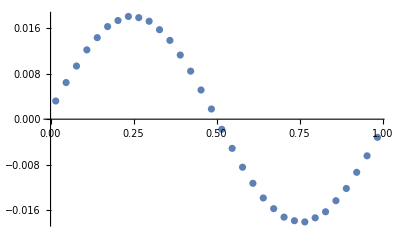

```mathematica
ListPlot[sol2]
```

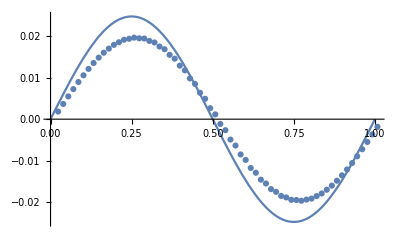

```mathematica
Show[ListPlot[sol2],Plot[u[x],{x,0,1}],PlotRange->All]
```

```mathematica
sol={0.00183729,0.00366281,0.00547368,0.00722858,0.00893752,0.0105563,0.0120896,0.0135145,0.0148035,0.0159858,0.0169703,0.0178723,0.0185033,0.0190984,0.0193407,0.0196144,0.019448,0.0193981,0.0188195,0.0184553,0.0174778,0.01682,0.0154731,0.0145529,0.0128808,0.0117386,0.009799,0.00848314,0.0063443,0.00490914,0.00264747,0.00115158,-0.0011515,-0.0026474,-0.0049091,-0.0063443,-0.0084831,-0.009799,-0.0117386,-0.0128808,-0.0145529,-0.0154731,-0.01682,-0.0174778,-0.0184553,-0.0188195,-0.0193981,-0.019448,-0.0196144,-0.0193407,-0.0190984,-0.0185033,-0.0178723,-0.0169703,-0.0159858,-0.0148035,-0.0135145,-0.0120896,-0.0105563,-0.00893752,-0.00722858,-0.00547368,-0.00366281,-0.00183729};
```

```mathematica
sol={0.000348715,0.000690765,0.00101076,0.00131627,0.00160002,0.00187306,0.00212301,0.00235838,0.00256765,0.00275803,0.00292009,0.00305891,0.00316734,0.00324897,0.00329968,0.00332104,0.0033117,0.0032713,0.00320189,0.00310127,0.00297425,0.00281661,0.00263627,0.00242757,0.00220076,0.0019483,0.00168286,0.00139618,0.00110253,0.0007922,0.000480762,0.000158498,-0.000158498,-0.000480762,-0.0007922,-0.00110253,-0.00139618,-0.00168286,-0.0019483,-0.00220076,-0.00242757,-0.00263627,-0.00281661,-0.00297425,-0.00310127,-0.00320189,-0.0032713,-0.0033117,-0.00332104,-0.00329968,-0.00324897,-0.00316734,-0.00305891,-0.00292009,-0.00275803,-0.00256765,-0.00235838,-0.00212301,-0.00187306,-0.00160002,-0.00131627,-0.00101076,-0.000690765,-0.000348715};
sol2 = Table[{1/64(i + 0.5),sol[[i]]},{i,1,64}];
```

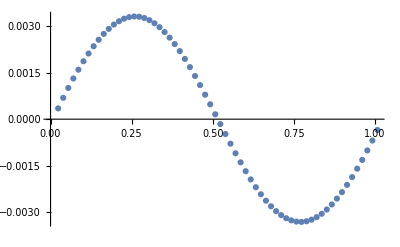

```mathematica
ListPlot[sol2]
```

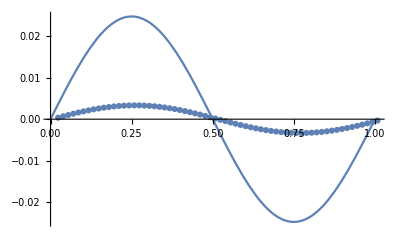

```mathematica
Show[ListPlot[sol2],Plot[u[x],{x,0,1}],PlotRange->All]
```

```mathematica
sol={0.0020112,0.00401448,0.00599002,0.00791827,0.00978016,0.0115572,0.0132319,0.0147876,0.0162088,0.0174814,0.0185927,0.0195316,0.0202887,0.0208562,0.0212283,0.0214011,0.0213725,0.0211425,0.020713,0.0200878,0.0192725,0.0182748,0.017104,0.015771,0.0142884,0.0126701,0.0109316,0.0090893,0.00716062,0.0051639,0.0031181,0.00104267,-0.00104267,-0.0031181,-0.0051639,-0.00716062,-0.0090893,-0.0109316,-0.0126701,-0.0142884,-0.015771,-0.017104,-0.0182748,-0.0192725,-0.0200878,-0.020713,-0.0211425,-0.0213725,-0.0214011,-0.0212283,-0.0208562,-0.0202887,-0.0195316,-0.0185927,-0.0174814,-0.0162088,-0.0147876,-0.0132319,-0.0115572,-0.00978016,-0.00791827,-0.00599002,-0.00401448,-0.0020112};
sol2 = Table[{1/64(i + 0.5),sol[[i]]},{i,1,64}];
```

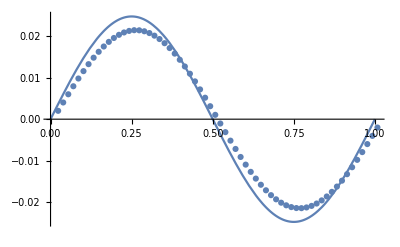

```mathematica
Show[ListPlot[sol2],Plot[u[x],{x,0,1}],PlotRange->All]
```

```mathematica
Maximize[u[x],x]
```

```mathematica
{1/(1+4 π^2),{x->1/4}}//N
```

{0.0247045,{x→0.25}}

```mathematica
Clear[x]
```

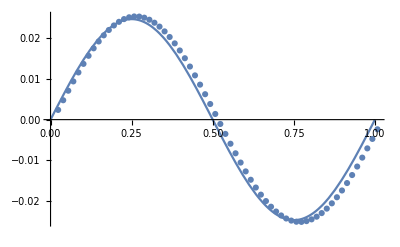

{0.00227471,0.00436871,0.00593984,0.0067261,0.00658544,0.00551733,0.00366269,0.00128243,-0.00128243,-0.00366269,-0.00551733,-0.00658544,-0.0067261,-0.00593984,-0.00436871,-0.00227471}

```mathematica
sol = {0.00238938,0.00476742,0.00711087,0.00939683,0.011603,0.0137077,0.0156904,0.0175317,0.0192134,0.0207192,0.0220341,0.0231451,0.0240413,0.0247137,0.0251554,0.025362,0.025331,0.0250625,0.0245587,0.0238241,0.0228655,0.0216918,0.0203139,0.0187449,0.0169994,0.0150939,0.0130465,0.0108765,0.00860452,0.00625206,0.00384143,0.00139551,-0.0010625,-0.00350928,-0.00592163,-0.00827665,-0.010552,-0.0127263,-0.0147787,-0.01669,-0.0184421,-0.0200185,-0.0214044,-0.0225869,-0.0235549,-0.0242995,-0.0248139,-0.0250936,-0.0251363,-0.0249419,-0.0245127,-0.0238533,-0.0229705,-0.0218731,-0.0205722,-0.0190806,-0.0174132,-0.0155865,-0.0136185,-0.0115286,-0.00933736,-0.00706629,-0.00473773,-0.00237457};
sol2 = Table[{1/64(i + 0.5),sol[[i]]},{i,1,64}];
Show[ListPlot[sol2],Plot[u[x],{x,0,1}],PlotRange->All]
```

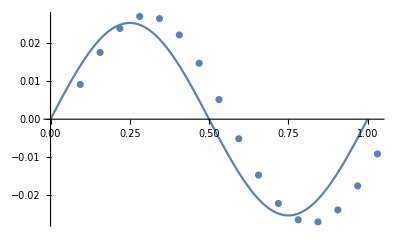

```mathematica
m= 16;
u[x_]:=1/(4 π^2 + h^2)Sin[2π x]
h = (b - a)/m;
x = Table[h*(i - 0.5),{i,1,m}];
f[x_]:=h^2*Sin[2 π x];
exactSol= LinearSolve[A[m],rhsList[[2]]];
exactSol= LinearSolve[A[m],f[x]];
sol2 = Table[{1/m(i + 0.5),exactSol[[i]]},{i,1,m}];
Show[ListPlot[sol2],Plot[u[x],{x,0,1}],PlotRange->All]
```

```mathematica
f[x]
```

{0.00597943,0.0144356,0.0144356,0.00597943,-0.00597943,-0.0144356,-0.0144356,-0.00597943}

```mathematica
rhsList[[3]]
```

{0.000364769,0.000880629,0.000880629,0.000364769,-0.000364769,-0.000880629,-0.000880629,-0.000364769}

```mathematica
Norm[f[x]-rhsList[[3]]]/Norm[f[x]]
```

0.938996